```mathematica
sol = DSolve[{r'[t]==-r[t], o'[t] ==1/Log[r[t]]}, {r[t], o[t]}, t]
```

{{r[t]→ⅇ^-t C[1],o[t]→C[2]-Log[Log[ⅇ^-t C[1]]]}}

```mathematica
r[t_]:=ⅇ^-t
o[t_]:=1-Log[Log[ⅇ^-t]]
```

```mathematica
Limit[o[t], t-> Infinity]
```

-∞

```mathematica
a[x_, y_] :=-x-y/(Log[Sqrt[x^2 + y^2]]) 
b[x_, y_] :=-y+x/(Log[Sqrt[x^2 + y^2]])
```

```mathematica
xx[x_, y_] := Evaluate[D[a[x, y], x]]
xy[x_, y_] := Evaluate[D[a[x, y], y]]
yx[x_, y_] := Evaluate[D[b[x, y], x]]
yy[x_, y_] := Evaluate[D[b[x, y], y]]
```

```mathematica
Limit[xx[x, y], {x->0, y->0}]
Limit[xy[x, y], {x->0, y->0}]
Limit[yx[x, y], {x->0, y->0}]
Limit[yy[x, y], {x->0, y->0}]
```

-1

0

0

-1

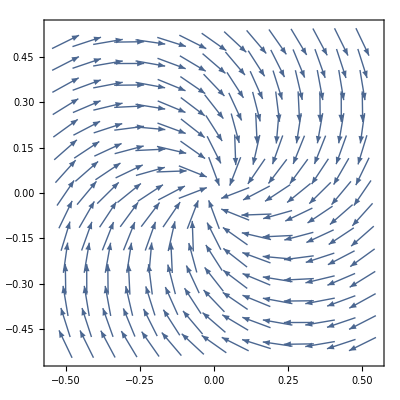

```mathematica
VectorPlot[{a[x, y], b[x, y]}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, VectorScale->{Automatic,Automatic,None}]
```